```mathematica
δ=1.;
A={{1,0,δ,0},{0,1,0,δ},{0,0,1,0},{0,0,0,1}};
B={{0,0},{0,0},{δ,0},{0,δ}};
Q={{1,0,0,0},{0,1,0,0},{0,0,0,0},{0,0,0,0}};
R=δ^4{{1,0},{0,1}};
P=DiscreteRiccatiSolve[{A,B},{Q,R}];
H=B.Inverse[R+Transpose[B].P.B].Transpose[B];
F=A-H.P.A;
```

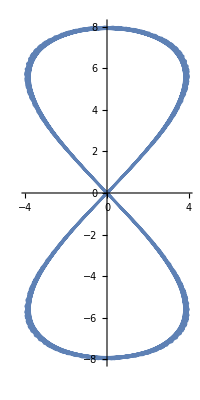

```mathematica
T=200;
g[t_]:=8{Sin[t]Cos[t],Sin[t]};
f[t_]:=g[t/3];
d=Table[Join[f[t],{0,0}],{t,0,T}];
ListLinePlot[#[[1;;2]]&/@d,AspectRatio->Automatic]
w=Table[A.d[[t]]-d[[t+1]]+RandomReal[{-1,1},4],{t,1,T}]//N;
w=Join[ConstantArray[{0,0,0,0},T],w,ConstantArray[{0,0,0,0},T]];
x0={0,0,0,0};
```

{9270.93,4221.62,1146.29,492.475,483.82}

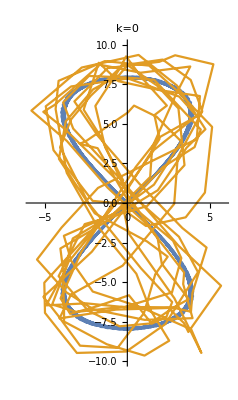
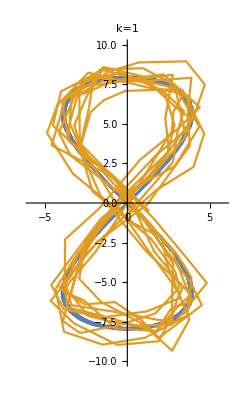
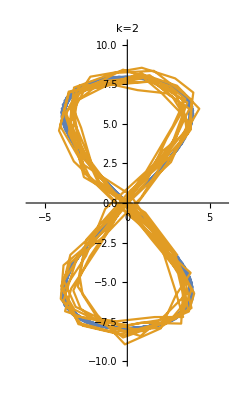
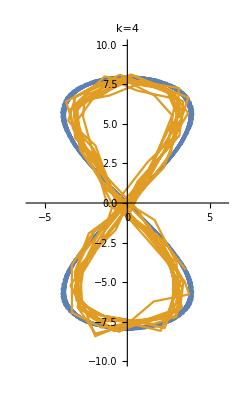
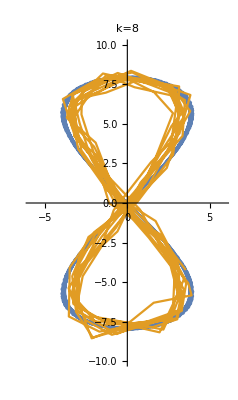

```mathematica
plotlist={};
Table[
uu[x_,w_]:=-Inverse[R+Transpose[B].P.B].Transpose[B].(P.A.x+Sum[MatrixPower[Transpose[F],i].P.w[[i+1]],{i,0,k-1}]);
xx[x_,w_]:=A.x+B.uu[x,w]+w[[1]];
path=FoldPairList[{{xx[#1,#2],uu[#1,#2]},xx[#1,#2]}&,x0,Table[w[[T+i;;T+i+Max[0,k-1]]],{i,1,T}]];
xpath=#[[1]]&/@path;
PrependTo[xpath,x0];
AppendTo[plotlist,ListLinePlot[{#[[1;;2]]&/@d,#[[1;;2]]&/@(xpath+d)},PlotRange->{{-5.9,5.9},{-9.9,9.9}},AspectRatio->Automatic,PlotLabel->"k="<>ToString[k],LabelStyle->{FontSize->30},Ticks->None]];
Export["eight-tracking_"<>ToString[k]<>".pdf",plotlist[[-1]]];
upath=#[[2]]&/@path;
Total[#.Q.#&/@xpath]+Total[#.R.#&/@upath],{k,{0,1,2,4,8}}]
plotlist
```

```mathematica
k=T;
uu[x_,w_]:=-Inverse[R+Transpose[B].P.B].Transpose[B].(P.A.x+Sum[MatrixPower[Transpose[F],i].P.w[[i+1]],{i,0,k-1}]);
xx[x_,w_]:=A.x+B.uu[x,w]+w[[1]];
path=FoldPairList[{{xx[#1,#2],uu[#1,#2]},xx[#1,#2]}&,x0,Table[w[[T+i;;T+i+Max[0,k-1]]],{i,1,T}]];
xpath=#[[1]]&/@path;
(*ListLinePlot[Prepend[xpath,x0],PlotRange->All]*)
upath=#[[2]]&/@path;
offlinecost=Total[#.Q.#&/@xpath]+Total[#.R.#&/@upath]
```

483.805

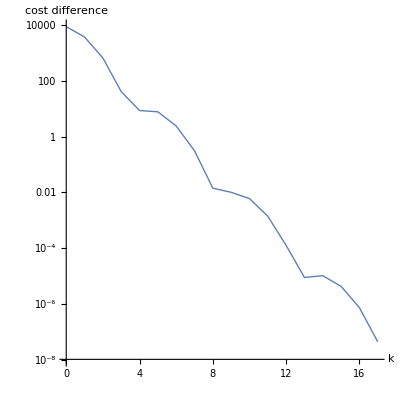

cost_diff.pdf

```mathematica
costlist={};
For[k=0,k<18,k++,
uu[x_,w_]:=-Inverse[R+Transpose[B].P.B].Transpose[B].(P.A.x+Sum[MatrixPower[Transpose[F],i].P.w[[i+1]],{i,0,k-1}]);
xx[x_,w_]:=A.x+B.uu[x,w]+w[[1]];
path=FoldPairList[{{xx[#1,#2],uu[#1,#2]},xx[#1,#2]}&,x0,Table[w[[T+i;;T+i+Max[0,k-1]]],{i,1,T}]];
xpath=#[[1]]&/@path;
(*ListLinePlot[Prepend[xpath,x0],PlotRange->All]*)
upath=#[[2]]&/@path;
(*ListLinePlot[Table[{i-1,upath[[i,1]]},{i,1,T}],PlotRange->All]*)
AppendTo[costlist,{k,(Total[#.Q.#&/@xpath]+Total[#.R.#&/@upath])-offlinecost}]]
ListLinePlot[costlist,AxesLabel->{"k","cost difference"},LabelStyle->{FontSize->26},AspectRatio->1,PlotStyle->Thick,ScalingFunctions->"Log"]
Export["cost_diff.pdf",%]
```